# Examples

## Cylinder on inclined slope

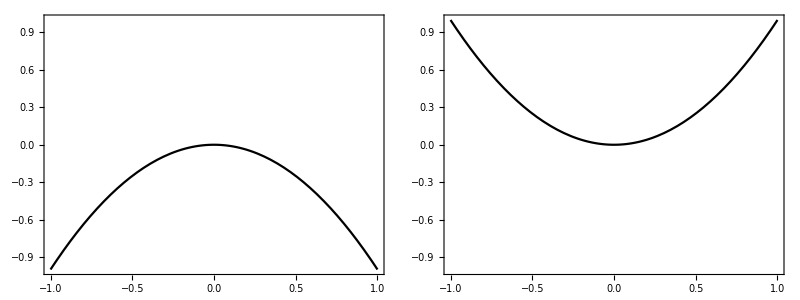

```mathematica
Grid[{{
Plot[-x^2,{x,-1,1},PlotRange->{{-1,1},{-1,1}},AspectRatio->Automatic,Frame->True,PlotStyle->Black,ImageSize->300],

Plot[x^2,{x,-1,1},PlotRange->{{-1,1},{-1,1}},AspectRatio->Automatic,Frame->True,PlotStyle->Black,ImageSize->300]}}]
```

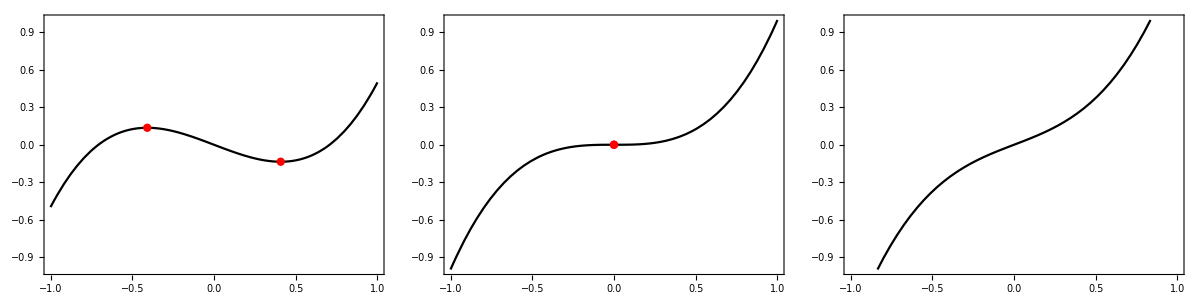

```mathematica
Grid[{Table[
Show[
Plot[x^3+u x,{x,-1,1},ImageSize->300,Frame->True,PlotStyle->Black,AspectRatio->Automatic,PlotRange->{{-1,1},{-1,1}}],
ListPlot[{x,x^3+u x}/.Solve[3 x^2+u==0,x],PlotStyle->{Red,PointSize[0.02]}]
]
,{u,{-0.5,0,0.5}}]}]
```

## Zeeman catastrophe machine

```mathematica
{u,v}/.Solve[
{D[x^4-u x^2+v x,x]==0,
D[x^4-u x^2+v x,x,x]==0},{u,v}]⟦1⟧
```

{6 x^2,8 x^3}

```mathematica
Show[
ContourPlot3D[4 x^3-2 u x+v==0,{u,-1,1},{v,-1,1},{x,-1,1},AxesLabel->{"u","v","x"},ImageSize->300,PlotPoints->100,ViewPoint->{Top,Right},ContourStyle->{Opacity[0.2]},Ticks->None(*,Axes->True,AxesOrigin->{0,0,0}*)],
ParametricPlot3D[
{6 x^2,8 x^3,-1},{x,-1,1},PlotRange->{{-1,1},{-1,1}},PlotStyle->Red,ViewPoint->{Top,Right}],
ParametricPlot3D[
{6 x^2,8 x^3,x},{x,-1,1},PlotRange->{{-1,1},{-1,1}},PlotStyle->Blue,ViewPoint->{Top,Right}]
]
```

-Graphics3D-

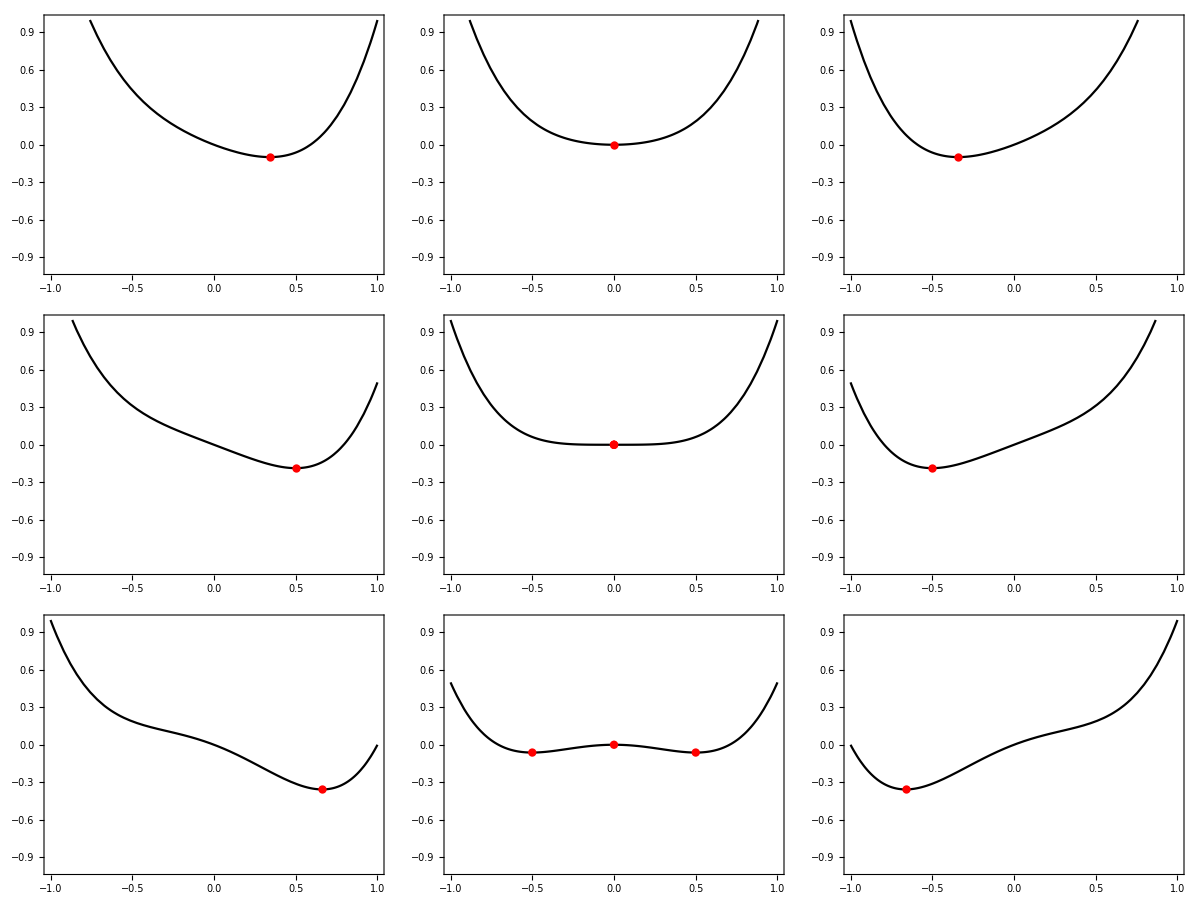

```mathematica
Grid[Table[
Show[
Plot[x^4-u x^2+v x,{x,-1,1},ImageSize->300,Frame->True,PlotStyle->Black,AspectRatio->Automatic,PlotRange->{{-1,1},{-1,1}}],
ListPlot[{x,x^4-u x^2+v x}/.Solve[4 x^3-2u x+v==0,x],PlotStyle->{Red,PointSize[0.02]}]
]
,{u,{-0.5,0,0.5}},{v,{-0.5,0,0.5}}]
]
```

## Optics circular mirror

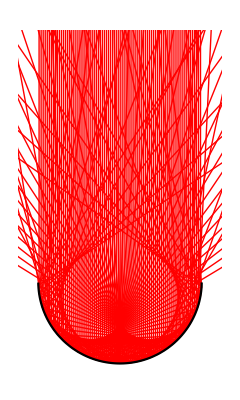

```mathematica
n=Normalize[{-D[-√(1-x^2),x],1}]/. x->x[t];
vreflect=-1.99 ({x'[t],y'[t]}.n) n+{x'[t],y'[t]};

Show[
Show[Table[
Quiet[sol=NDSolveValue[{y''[t]==0,x''[t]==0,x'[0]==0,x[0]==b,y'[0]==-1,y[0]==4,WhenEvent[y[t]==Re[-√(1-x[t]^2)],{{x'[t],y'[t]}->Evaluate[vreflect]},"IntegrateEvent"->True]},{x,y},{t,0,20}]];
ParametricPlot[Evaluate[{sol⟦1⟧[t],sol⟦2⟧[t]}],{t,0,20},PlotRange->All,PlotStyle->{Red,Thin}]
,{b,-0.99,0.99,0.025}],PlotRange->{{-1.2,1.2},{-1,3}}],
Plot[-√(1-x^2),{x,-2,2},PlotStyle->Black],
Axes->False]
```

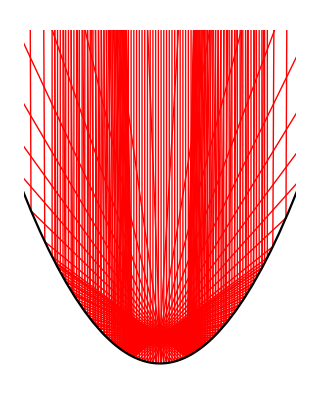

```mathematica
n=Normalize[{-D[x^2,x],1}]/. x->x[t];
vreflect=-(1.+.99) ({x'[t],y'[t]}.n) n+{x'[t],y'[t]};

Show[
Show[Table[
Quiet[sol=NDSolveValue[{y''[t]==0,x''[t]==0,x'[0]==0,x[0]==b,y'[0]==-1,y[0]==4,WhenEvent[y[t]==Re[x[t]^2],{{x'[t],y'[t]}->Evaluate[vreflect]},"IntegrateEvent"->True]},{x,y},{t,0,20}]];
ParametricPlot[Evaluate[{sol⟦1⟧[t],sol⟦2⟧[t]}],{t,0,20},PlotRange->All,PlotStyle->{Red,Thin}]
,{b,-0.99,0.99,0.025}],PlotRange->{{-1.2,1.2},{0,3}}],
Plot[x^2,{x,-2,2},PlotStyle->Black],
Axes->False]
```

```mathematica
solve[b_,number_]:=
Module[{i=0},
NDSolveValue[{y''[t]==0,x''[t]==0,x'[0]==0,x[0]==b,y'[0]==-1,y[0]==4,WhenEvent[x[t]^2+y[t]^2==1,{i++;
Switch[i,1,,number,"StopIntegration",
_,{x'[t],y'[t]}->Evaluate[-1.99 ({x'[t],y'[t]}.{x[t],y[t]}) {x[t],y[t]}+{x'[t],y'[t]}]]}
,"IntegrateEvent"->True]},{x,y},{t,0,10000}]]
```

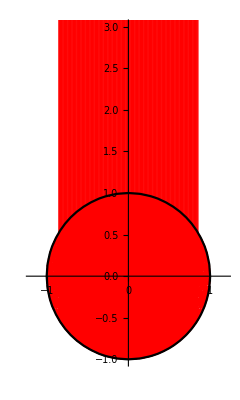

```mathematica
pathPlots=Show[Table[
Module[{sol=solve[b,6]},
ParametricPlot[Evaluate[{sol⟦1⟧[t],sol⟦2⟧[t]}],{t,0,sol⟦1⟧["Domain"]⟦1,2⟧},PlotRange->All,PlotStyle->{Red,Thin}]
],{b,-0.85,0.85,0.01}]];

Show[pathPlots,
ContourPlot[x^2+y^2==1,{x,-2,2},{y,-2,2},ContourStyle->Black],
PlotRange->{{-1.2,1.2},{-1,3}},Axes->True,AxesOrigin->{0,0}]
```

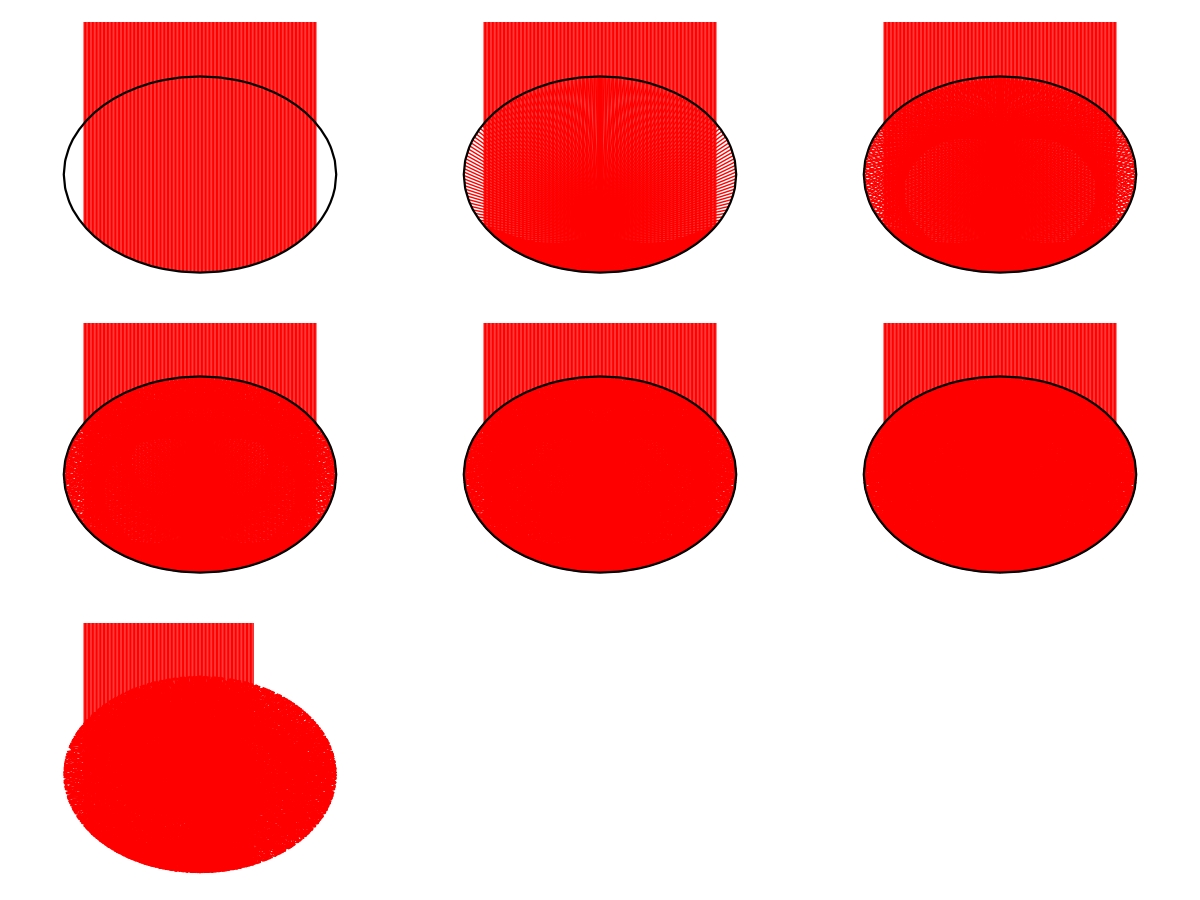

```mathematica
Monitor[Grid[
Partition[Table[
pathPlots=Show[Table[
Module[{sol=solve[b,number]},
ParametricPlot[Evaluate[{sol⟦1⟧[t],sol⟦2⟧[t]}],{t,0,sol⟦1⟧["Domain"]⟦1,2⟧},PlotRange->All,PlotStyle->{Red,Thin}]
]
,{b,-0.85,0.85,0.01}]];

Show[pathPlots,
ContourPlot[x^2+y^2==1,{x,-2,2},{y,-2,2},ContourStyle->Black],
PlotRange->{{-1.2,1.2},{-1,1.5}},ImageSize->300,Axes->False],{number,2,10}],3]],number]
```